{{1,-1.6500.023},{2,-1.9260.023},{3,-2.1790.023},{4,-2.4300.022},{5,-2.4980.022},{6,-2.7770.022},{7,-2.7050.021},{8,-2.6240.021},{9,-2.7730.021},{10,-2.7070.021}}

{{1,-1.9240.023},{2,-2.0000.023},{3,-1.9240.023},{4,-1.6020.024},{5,-1.4840.024},{6,-1.2190.024},{7,-1.1050.024},{8,-0.9280.024},{9,-0.8340.024},{10,-0.7000.024}}

{{1,-1.5580.023},{2,-1.4640.023},{3,-1.4320.023},{4,-1.4170.024},{5,-1.2900.024},{6,-1.3420.024},{7,-1.3060.024},{8,-1.0800.024},{9,-1.1090.024},{10,-0.7230.024}}

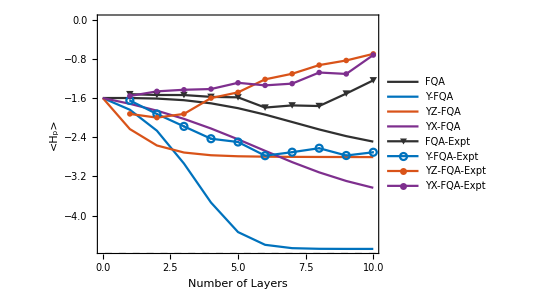

```mathematica
dataExpFP={-1.5215760714075468,-1.5379762920061082,-1.539383503308206,-1.576605419470415,-1.5863936332119242,-1.7951287675419525,-1.7508960264956936,-1.7636529831001009,-1.5095675260896377,-1.2392372804415812};
dataExpFPstd={0.023034779305663174,0.023090725509314517,0.023101670071699085,0.02306376768340287,0.02337035740995881,0.023136328960493575,0.023325385140158483,0.02317447150007315,0.02378087729186127,0.023731429806939968};
dataF={-1.6000000000000003,-1.6,-1.6112186988051767,-1.6443679258190123,-1.7083184185777482,-1.8074843875028677,-1.9385975788191365,-2.089294725356276,-2.2413472146032403,-2.3779707558615923,-2.49004185355962};
dataFCDyz={-1.6000000000000003,-2.2334470495899725,-2.5684083828392423,-2.7120386006966477,-2.767704374147625,-2.7886639605780035,-2.796901117668267,-2.800578573771387,-2.802597839473322,-2.8040150338739207,-2.8052546529514255};
dataFCDyx={-1.6000000000000003,-1.7181717682385587,-1.8581932932739278,-2.02558432100301,-2.2220256338980735,-2.4431561925077867,-2.677433835549765,-2.9078152120628245,-3.116836552173917,-3.2926242115193656,-3.431801610429116};
dataFCDy={-1.6000000000000003,-1.8392700229319439,-2.2666712462333316,-2.936265422867532,-3.732462126362557,-4.335154531302772,-4.59504045908713,-4.663320886131266,-4.676413580330181,-4.678384780480009,-4.6785644797493005};
dataExpFCDyP={-1.6500233691776325,-1.9262380131145607,-2.178752673960533,-2.4304023391123537,-2.4977849773391663,-2.776810237040346,-2.7051242667555018,-2.6240316848897116,-2.7729851080613495,-2.7066816470175543};
dataExpFCDyPstd={0.022823084442213606,0.022676405727401514,0.022549961278398922,0.022015429856615303,0.02186006038728605,0.02174720969113031,0.021465450170911584,0.021398903439715723,0.021321433433828894,0.020989536200989492};
dataExpFCDyzP={-1.9244982224929141,-2.000223415800197,-1.9244140082342407,-1.6018077611530526,-1.4844063905162002,-1.2193633320667168,-1.1053862266474428,-0.928475986326299,-0.8341833619846335,-0.6995894217577487};
dataExpFCDyzPstd={0.023153570271791442,0.023086926100068027,0.023207169066012938,0.023702866970723054,0.023692756035898502,0.024055203902370266,0.023999344141442405,0.02424805780665985,0.024158588691810215,0.024132870010769338};
dataExpFCDyxP={-1.5584578814029637,-1.4642625789547405,-1.43186357825864,-1.4169094110357756,-1.2896110577678075,-1.3420917669563954,-1.3063679718183718,-1.0799244304234838,-1.108759423270031,-0.722856802771484};
dataExpFCDyxPstd={0.023013288908453097,0.023227652622800337,0.023418335930755343,0.023592983602393838,0.023817002100177783,0.02386531871118291,0.02391339301555325,0.024244744282961733,0.02421546080611363,0.024440397760232817};
dataExpFPp=Table[{i,Around[dataExpFP[[i]],dataExpFPstd[[i]]]},{i,Length[dataExpFP]}];
dataExpFCDyPp=Table[{i,Around[dataExpFCDyP[[i]],dataExpFCDyPstd[[i]]]},{i,Length[dataExpFP]}]
dataExpFCDyzPp=Table[{i,Around[dataExpFCDyzP[[i]],dataExpFCDyzPstd[[i]]]},{i,Length[dataExpFP]}]
dataExpFCDyxPp=Table[{i,Around[dataExpFCDyxP[[i]],dataExpFCDyxPstd[[i]]]},{i,Length[dataExpFP]}]
dataFp=Table[{i-1,dataF[[i]]},{i,Length[dataF]}];
dataFCDyP=Table[{i-1,dataFCDy[[i]]},{i,Length[dataFCDy]}];
dataFCDyzP=Table[{i-1,dataFCDyz[[i]]},{i,Length[dataFCDyz]}];
dataFCDyxP=Table[{i-1,dataFCDyx[[i]]},{i,Length[dataFCDyx]}];
Show[ListPlot[{dataFp,dataFCDyP,dataFCDyzP,dataFCDyxP,dataExpFPp,dataExpFCDyPp,dataExpFCDyzPp,dataExpFCDyxPp},PlotRange->All,Joined->{True,True,True,True,True,True,True,True},PlotMarkers->{None,None,None,None,Automatic,Automatic,Automatic,Automatic},PlotLegends->{"FQA","Y-FQA","YZ-FQA","YX-FQA","FQA-Expt","Y-FQA-Expt","YZ-FQA-Expt","YX-FQA-Expt"},PlotStyle->{RGBColor["#303030"],RGBColor["#0072BD"],RGBColor["#D95319"],RGBColor["#7E2F8E"],RGBColor["#303030"],RGBColor["#0072BD"],RGBColor["#D95319"],RGBColor["#7E2F8E"]},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,FrameLabel->{{HoldForm["<H_p>"],None},{HoldForm["Number of Layers"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}],Plot[-4.780861320010876,{x,-3,300},PlotStyle->{Gray,Dashed}],AspectRatio->3/4]
```